reactions and transitions: (0→S | Λ
S→0 | μ s
I1+S→2 I1 | β_1 i_1 s
I2+S→2 I2 | β_2 i_2 s
I1+I2→I12 | δ i_1 i_2
I1+I12→I2 | η_1 i_1 i_12
I12+I2→I1 | η_2 i_12 i_2
I1→0 | i_1 μ_1
I2→0 | i_2 μ_2
I12→0 | i_12 μ_12)

siphons are{{i1,i2},{i1,i12},{i2,i12}}E0 is{s→Λ/μ} R1,R2, ... are{(β_2 Λ)/(μ μ_2),(β_1 Λ)/(μ μ_1)}

K=((β_1 s)/μ_1 | 0 | 0
0 | 0 | 0
0 | 0 | (β_2 s)/μ_2)ElTRat={{{i_2→-(-Λ+(μ μ_2)/β_2)/μ_2,s→μ_2/β_2,i_1→0,i_12→0}},{{i_1→-(-Λ+(μ μ_1)/β_1)/μ_1,s→μ_1/β_1,i_2→0,i_12→0}}} Jx=(-β_1 i_1-β_2 i_2-μ | -β_1 s | -β_2 s | 0
β_1 i_1 | -η_1 i_12-δ i_2-μ_1+β_1 s | -δ i_1+η_2 i_12 | -η_1 i_1+η_2 i_2
β_2 i_2 | η_1 i_12-δ i_2 | -δ i_1-η_2 i_12-μ_2+β_2 s | η_1 i_1-η_2 i_2
0 | -η_1 i_12+δ i_2 | δ i_1-η_2 i_12 | -η_1 i_1-η_2 i_2-μ_12)

Minimal siphons: {T_1→{i1,i2},T_2→{i1,i12},T_3→{i2,i12}}

IGMS edges: {1->2,1->3,2->1,2->3,3->1,3->2}

Cycles found: 5

Cycles: {{2->3,3->2},{1->3,3->1},{1->2,2->1},{1->3,3->2,2->1},{1->2,2->3,3->1}}

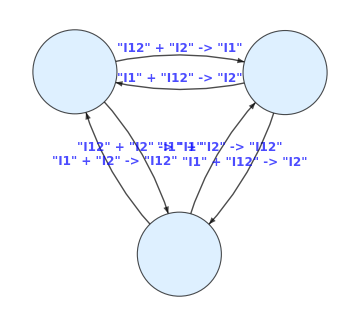

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];SetOptions[$FrontEndSession,NotebookAutoSave->True];
NotebookSave[];
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"Dropbox","EpidCRNmodels"}]];Needs["EpidCRN`"];(*Get["HopfE`"];*)
(*Latex dictionary*)
Format[mu]:=μ;Format[de]:=δ;
Format[ga]:=ga;Format[ga1]:=Subscript[γ,1];Format[ga2]:=Subscript[γ,2];
Format[ga12]:=Subscript[γ,12];Format[ga2]:=Subscript[γ,21];
Format[th1]:=Subscript[θ,1];Format[th2]:=Subscript[θ,2];Format[th3]:=Subscript[θ,12];Format[thv]:=Subscript[θ,v];
Format[th]:=θ;
Format[La]:=Λ;Format[LaP]:=Subscript[Λ,p];
Format[be1]:=Subscript[β,1];Format[be2]:=Subscript[β,2];
Format[be12]:=Subscript[β,12];Format[be21]:=Subscript[β,21];
Format[de1]:=Subscript[δ,1];Format[de2]:=Subscript[δ,2];
Format[de12]:=Subscript[δ,12];Format[de21]:=Subscript[δ,21];
Format[deS]:=Subscript[δ,s];
Format[mu1]:=Subscript[μ,1];Format[mu2]:=Subscript[μ,2];
Format[mu12]:=Subscript[μ,12];Format[mu21]:=Subscript[μ,21];
Format[al1]:=Subscript[α,1];Format[al2]:=Subscript[α,2];Format[alv]:=Subscript[α,v];Format[si]:=σ;Format[rh]:=ρ;
Format[si1]:=Subscript[σ,1];Format[si2]:=Subscript[σ,2];
Format[et1]:=Subscript[η,1];Format[et2]:=Subscript[η,2];
Format[i1]:=Subscript[i,1];Format[i2]:=Subscript[i,2];
Format[i12]:=Subscript[i,12];Format[i21]:=Subscript[i,21];
Format[r1]:=Subscript[r,1];Format[r2]:=Subscript[r,2];Format[r12]:=Subscript[r,12];
RN = {
  0 -> "S",
  "S" -> 0,
  "S" + "I1" -> 2*"I1",
  "S" + "I2" -> 2*"I2",
  "I1" + "I2" -> "I12",
  "I1" + "I12" -> "I2",
  "I2" + "I12" -> "I1",
  "I1" -> 0,
  "I2" -> 0,
  "I12" -> 0
};

rts = {
  La,             (* birth *)
  mu*s,           (* S death *)
  be1*s*i1,       (* inf. i1 *)
  be2*s*i2,       (* inf. i12 *)
  de*i1*i2,       (* i1+i12->i12 *)
  et1*i1*i12,     (* i1+i12->i12 *)
  et2*i2*i12,     (* i12+i12->i1 *)
  mu1*i1,         (* i1 death *)
  mu2*i2,         (* i12 death *)
  mu12*i12        (* i12 death *)
};
Print["reactions and transitions: ",Transpose[{RN,rts}]//MatrixForm]
(*Get bdAn outputs*)

{RHS, var, par, cp, mSi, Jx, Jy, E0, K, R0A, infV,alp, bet,gam, ElTRat} = bdCo[RN, rts];
Print["siphons are",mSi,"E0 is",E0," R1,R2, ... are",R0A/.E0]
jac=Grad[RHS,var];Print["K=",K//MatrixForm,"ElTRat=",ElTRat," Jx=",Jx//MatrixForm];
IGMS[RN, mSi];
(*so=Solve[RHS==0,var]*)
```

reactions and transitions: (0→S | Λ
S→0 | μ s
I1+S→2 I1 | β_1 i_1 s
I2+S→2 I2 | β_2 i_2 s
I1+I2→2 I12 | δ i_1 i_2
I1+I12→2 I2 | η_1 i_1 i_12
I12+I2→2 I1 | η_2 i_12 i_2
I1→0 | i_1 μ_1
I2→0 | i_2 μ_2
I12→0 | i_12 μ_12)

(Λ-β_1 i_1 s-β_2 i_2 s-μ s
-η_1 i_1 i_12-δ i_1 i_2+2 η_2 i_12 i_2-i_1 μ_1+β_1 i_1 s
2 η_1 i_1 i_12-δ i_1 i_2-η_2 i_12 i_2-i_2 μ_2+β_2 i_2 s
-η_1 i_1 i_12+2 δ i_1 i_2-η_2 i_12 i_2-i_12 μ_12)

siphons are{{i1,i2},{i1,i12},{i2,i12}}E0 is{s→Λ/μ} R1,R2, ... are{(β_2 Λ)/(μ μ_2),(β_1 Λ)/(μ μ_1)}

K=((β_1 s)/μ_1 | 0 | 0
0 | 0 | 0
0 | 0 | (β_2 s)/μ_2)ElTRat={{},{{i_2→-(-Λ+(μ μ_2)/β_2)/μ_2,s→μ_2/β_2,i_1→0,i_12→0}},{{i_1→-(-Λ+(μ μ_1)/β_1)/μ_1,s→μ_1/β_1,i_2→0,i_12→0}}} Jx=(-β_1 i_1-β_2 i_2-μ | -β_1 s | -β_2 s | 0
β_1 i_1 | -η_1 i_12-δ i_2-μ_1+β_1 s | -δ i_1+2 η_2 i_12 | -η_1 i_1+2 η_2 i_2
β_2 i_2 | 2 η_1 i_12-δ i_2 | -δ i_1-η_2 i_12-μ_2+β_2 s | 2 η_1 i_1-η_2 i_2
0 | -η_1 i_12+2 δ i_2 | 2 δ i_1-η_2 i_12 | -η_1 i_1-η_2 i_2-μ_12)

Minimal siphons: {T_1→{i1,i2},T_2→{i1,i12},T_3→{i2,i12}}

IGMS edges: {1->2,1->3,2->1,2->3,3->1,3->2}

Cycles found: 5

Cycles: {{2->3,3->2},{1->3,3->1},{1->2,2->1},{1->3,3->2,2->1},{1->2,2->3,3->1}}

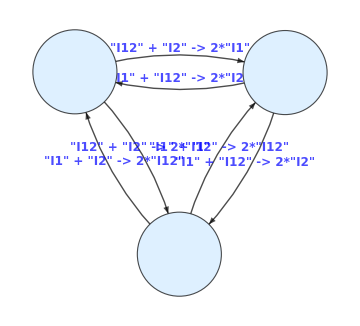

```mathematica
RN = {
  0 -> "S",
  "S" -> 0,
  "S" + "I1" -> 2*"I1",
  "S" + "I2" -> 2*"I2",
  "I1" + "I2" -> 2*"I12",
  "I1" + "I12" -> 2*"I2",
  "I2" + "I12" -> 2*"I1",
  "I1" -> 0,
  "I2" -> 0,
  "I12" -> 0
};

rts = {
  La,             (* birth *)
  mu*s,           (* S death *)
  be1*s*i1,       (* inf. i1 *)
  be2*s*i2,       (* inf. i12 *)
  de*i1*i2,       (* i1+i12->i12 *)
  et1*i1*i12,     (* i1+i12->i12 *)
  et2*i2*i12,     (* i12+i12->i1 *)
  mu1*i1,         (* i1 death *)
  mu2*i2,         (* i12 death *)
  mu12*i12        (* i12 death *)
};
Print["reactions and transitions: ",Transpose[{RN,rts}]//MatrixForm]
(*Get bdAn outputs*)

{RHS, var, par, cp, mSi, Jx, Jy, E0, K, R0A, infV,alp, bet,gam, ElTRat} = bdCo[RN, rts];
RHS//MatrixForm
Print["siphons are",mSi,"E0 is",E0," R1,R2, ... are",R0A/.E0]
jac=Grad[RHS,var];
Print["K=",K//MatrixForm,"ElTRat=",ElTRat," Jx=",Jx//MatrixForm];
IGMS[RN, mSi];
(*so=Solve[RHS==0,var]*)
```

```mathematica
Jx-Jx1//Factor//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | -η_2 i_12 | -η_2 i_2
0 | -η_1 i_12 | 0 | -η_1 i_1
0 | -δ i_2 | -δ i_1 | 0)

```mathematica
Export["LiScan.pdf",fPl]
```

LiScan.pdf